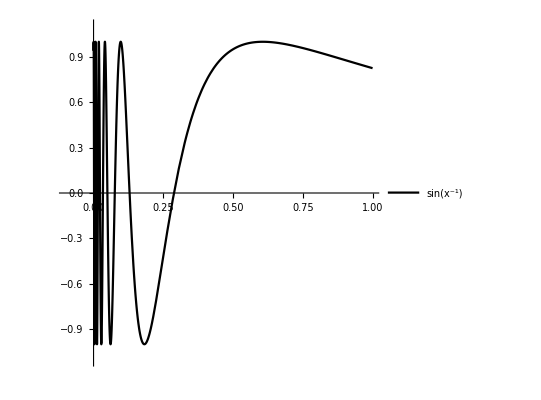

```mathematica
sin=Plot[{Sin[1/(x+0.03)]},
{x,0,1},
MaxRecursion->12,
AspectRatio->1,
Ticks->None,
PlotRange->{{-0.1,1},{-1.1,1.1}},
LabelStyle->(FontFamily->"STIX Two Text"),
PlotStyle->{Black},
PlotLegends->{Sin[Superscript[x,-1]]}]
```

```mathematica
text=Graphics[{Red, Style[Text[V,{-0.03,0.3}], FontFamily->"STIX Two Text",Italic],LabelStyle-> (FontFamily->"STIX Two Text")}]
```

-Graphics-

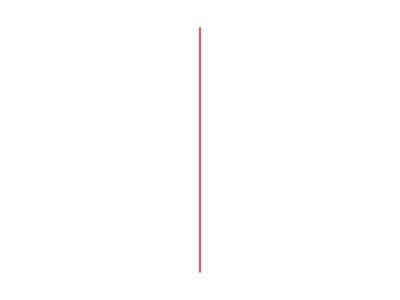

```mathematica
line=Graphics[{Thick,Red,Line[{{0,-1},{0,1}}]}]
```

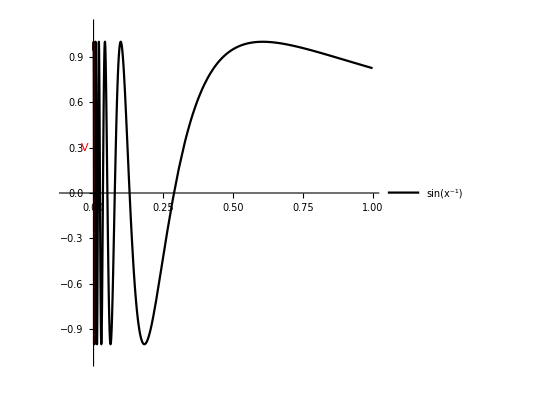

```mathematica
res=Show[sin,line,text]
```

```mathematica
Export["D:\\wolfram\\sinXinv.pdf",res]
```

D:\wolfram\sinXinv.pdf